```mathematica
M[tdots_,Gamma1_,Gamma2_] := tdots -I*Sqrt[Gamma1*Gamma2]
```

```mathematica
M2[tdots_,Gamma1_,Gamma2_] :=(M[tdots,Gamma1,Conjugate[Gamma2]])^2
```

M[Conjugate[tdots],Conjugate[Gamma1],Gamma2]

```mathematica
DQD[w_ ,e1_, e2_, tdots_,Gamma1_,Gamma2_]:= (1/(w -e1+Gamma1*I -M2[tdots,Gamma1,Gamma2]/(w -e2+I*Gamma2)))
```

```mathematica
Copl[w_ , em_]:=w/(w+em)
```

```mathematica
M5[w_ ,e2_, tdots_,Gamma1_,Gamma2_,t1_,t2_]:=(t1+(t2 * M[tdots,Gamma1,Gamma2])/(w-e2+I*Gamma2))
```

```mathematica
M25[w_ ,e2_, tdots_,Gamma1_,Gamma2_,t1_,t2_] :=M5[w ,e2, tdots,Gamma1,Conjugate[Gamma2],t1,t2] *M5[w ,e2, Conjugate[tdots],Conjugate[Gamma1],Gamma2,Conjugate[t1],Conjugate[t2]]
```

```mathematica
Gff[w_ ,em_,e1_, e2_, tdots_,Gamma1_,Gamma2_,t1_,t2_]:= (1/(w-em-Copl[w, em]*((t2* Conjugate[t2])/(w-e2+I*Gamma2)+(t2* Conjugate[t2])/(w+e2+I*Gamma2)+M25[w ,-e2, -tdots,Gamma1,Conjugate[Gamma2],-t1,-t2]*DQD[w,-e1, -e2, -tdots,Gamma1,Gamma2])))
```

```mathematica
DOS1[w_ ,em_,e1_, e2_, tdots_,Gamma1_,Gamma2_,t1_,t2_]:= (1/((DQD[w,e1, e2, tdots,Gamma1,Gamma2])^(-1)-Copl[w, em]*(M25[w ,e2, tdots,Gamma1,Conjugate[Gamma2],t1,t2]*Gff[w ,em,e1, e2, tdots,Gamma1,Gamma2,t1,t2])))
```

```mathematica
Manipulate[

Plot[{-Im[DOS1[w,em,e1,e2, tdots,gamma1,gamma2,t1,t2]/Pi],-Im[DQD[w,e1,e2, tdots,gamma1,gamma2]/Pi]},{w,-a,a},PlotRange->All,PlotLabel->ToString[StringForm["Gamma1=`1`,Gamma2=`2`,tdots=`3`,t1=`4`,t2=`5`",gamma1,gamma2,tdots,t1,t2]],PlotLegends->{"down","up"}],{a,0.001,1},{gamma1,0,1*G,1*G}, {gamma2,0,4*G},{tdots,0,2*G},{t1, 0,4*G},{t2,0,4*G},{em,0,4*G},{e1, 0,0.2},{e2, 0,0.2}  ]
```

```mathematica
G = 0.0282691
```

0.0282691

0.02

```mathematica
/home/cifucito/nrgcode/TwoChNRG/Data/Gamma1=0.0282691,Gamma2=0.,tdots=0.02,t1=0.,t2=0.02.dat
```

1

```mathematica
Export[ToString[StringForm["/home/cifucito/nrgcode/TwoChNRG/Data/Green/Gamma1=`1`,Gamma2=`2`,tdots=`3`,t1=`4`,t2=`5`.dat",g1,g2,tt,m1,m2]],Table[Im[(-DOS1[o,0,0,0, tt,g1,g2,m1,m2])/Pi]],"Table"]
```

```mathematica
Export["/home/cifucito/nrgcode/TwoChNRG/Data/DQD",Table[Im[(-DQD[o,0,0, tt,g1,g2])/Pi]],"Table"]
```

/home/cifucito/nrgcode/TwoChNRG/Data/DQD

```mathematica
Table[Im[(-DQD[o,0,0, tt,g1,g2])/Pi]]
```

{0.112598,0.113506,0.114425,0.115356,0.116297,0.11725,0.118215,0.119192,0.120181,0.121183,0.122197,0.123224,0.124264,0.125317,0.126383,0.127463,0.128557,0.129665,0.130788,0.131925,0.133077,0.134245,0.135427,0.136626,0.13784,0.139071,0.140318,0.141582,0.142863,0.144162,0.145478,0.146813,0.148166,0.149538,0.150929,0.152339,0.153769,0.15522,0.156691,0.158183,0.159697,0.161232,0.16279,0.16437,0.165974,0.167601,0.169252,0.170927,0.172628,0.174354,0.176106,0.177885,0.17969,0.181524,0.183385,0.185276,0.187195,0.189145,0.191125,0.193137,0.19518,0.197256,0.199366,0.201509,0.203687,0.205901,0.208151,0.210438,0.212763,0.215127,0.21753,0.219974,0.222459,0.224986,0.227557,0.230172,0.232832,0.235539,0.238293,0.241096,0.243949,0.246852,0.249808,0.252817,0.255881,0.259,0.262178,0.265414,0.26871,0.272068,0.275489,0.278975,0.282528,0.286149,0.28984,0.293603,0.29744,0.301352,0.305342,0.309412,0.313563,0.317799,0.322121,0.326532,0.331034,0.33563,0.340322,0.345113,0.350006,0.355004,0.360109,0.365326,0.370656,0.376104,0.381673,0.387366,0.393188,0.399142,0.405232,0.411462,0.417837,0.424361,0.43104,0.437877,0.444877,0.452047,0.459392,0.466916,0.474628,0.482531,0.490633,0.498941,0.507462,0.516202,0.52517,0.534374,0.543821,0.553521,0.563482,0.573714,0.584228,0.595032,0.606138,0.617558,0.629304,0.641386,0.65382,0.666618,0.679795,0.693366,0.707347,0.721754,0.736604,0.751917,0.767711,0.784007,0.800825,0.81819,0.836124,0.854652,0.873801,0.8936,0.914076,0.935262,0.95719,0.979896,1.00342,1.02779,1.05306,1.07927,1.10646,1.13469,1.16401,1.19447,1.22614,1.25908,1.29335,1.32903,1.3662,1.40493,1.44533,1.48747,1.53147,1.57743,1.62547,1.67571,1.72829,1.78336,1.84106,1.90157,1.96506,2.03173,2.1018,2.17548,2.25302,2.33469,2.42078,2.5116,2.60747,2.70878,2.81591,2.92929,3.0494,3.17672,3.31181,3.45526,3.60771,3.76984,3.94238,4.12614,4.32196,4.53071,4.75334,4.99081,5.24411,5.5142,5.80202,6.1084,6.43401,6.77924,7.1441,7.52799,7.92952,8.34617,8.77393,9.20683,9.63645,10.0514,10.4367,10.7737,11.0401,11.2105,11.2583,11.1581,10.8895,10.4408,9.81311,9.0219,8.09689,7.07892,6.01497,4.95248,3.93443,2.99615,2.16404,1.45606,0.883135,0.451075,0.162439,0.0180495,0.0180495,0.162439,0.451075,0.883135,1.45606,2.16404,2.99615,3.93443,4.95248,6.01497,7.07892,8.09689,9.0219,9.81311,10.4408,10.8895,11.1581,11.2583,11.2105,11.0401,10.7737,10.4367,10.0514,9.63645,9.20683,8.77393,8.34617,7.92952,7.52799,7.1441,6.77924,6.43401,6.1084,5.80202,5.5142,5.24411,4.99081,4.75334,4.53071,4.32196,4.12614,3.94238,3.76984,3.60771,3.45526,3.31181,3.17672,3.0494,2.92929,2.81591,2.70878,2.60747,2.5116,2.42078,2.33469,2.25302,2.17548,2.1018,2.03173,1.96506,1.90157,1.84106,1.78336,1.72829,1.67571,1.62547,1.57743,1.53147,1.48747,1.44533,1.40493,1.3662,1.32903,1.29335,1.25908,1.22614,1.19447,1.16401,1.13469,1.10646,1.07927,1.05306,1.02779,1.00342,0.979896,0.95719,0.935262,0.914076,0.8936,0.873801,0.854652,0.836124,0.81819,0.800825,0.784007,0.767711,0.751917,0.736604,0.721754,0.707347,0.693366,0.679795,0.666618,0.65382,0.641386,0.629304,0.617558,0.606138,0.595032,0.584228,0.573714,0.563482,0.553521,0.543821,0.534374,0.52517,0.516202,0.507462,0.498941,0.490633,0.482531,0.474628,0.466916,0.459392,0.452047,0.444877,0.437877,0.43104,0.424361,0.417837,0.411462,0.405232,0.399142,0.393188,0.387366,0.381673,0.376104,0.370656,0.365326,0.360109,0.355004,0.350006,0.345113,0.340322,0.33563,0.331034,0.326532,0.322121,0.317799,0.313563,0.309412,0.305342,0.301352,0.29744,0.293603,0.28984,0.286149,0.282528,0.278975,0.275489,0.272068,0.26871,0.265414,0.262178,0.259,0.255881,0.252817,0.249808,0.246852,0.243949,0.241096,0.238293,0.235539,0.232832,0.230172,0.227557,0.224986,0.222459,0.219974,0.21753,0.215127,0.212763,0.210438,0.208151,0.205901,0.203687,0.201509,0.199366,0.197256,0.19518,0.193137,0.191125,0.189145,0.187195,0.185276,0.183385,0.181524,0.17969,0.177885,0.176106,0.174354,0.172628,0.170927,0.169252,0.167601,0.165974,0.16437,0.16279,0.161232,0.159697,0.158183,0.156691,0.15522,0.153769,0.152339,0.150929,0.149538,0.148166,0.146813,0.145478,0.144162,0.142863,0.141582,0.140318,0.139071,0.13784,0.136626,0.135427,0.134245,0.133077,0.131925,0.130788,0.129665,0.128557,0.127463,0.126383,0.125317,0.124264,0.123224,0.122197,0.121183,0.120181,0.119192,0.118215,0.11725,0.116297,0.115356,0.114425,0.113506,0.112598}

```mathematica
NIntegrate[-Im[DOS1[w+I*0.000000001,0,0,0,(0.02/G),1,1,0,1]]/Pi,{w,-Infinity,Infinity}]
```

1.

```mathematica
NIntegrate[-Im[DOS1[w,0,0,0,0,1,2,2,1]]/Pi-Im[DOS1[w,0,0,0,0,2,1,1,2]]/Pi,{w,-Infinity,Infinity}]
```

1.5

```mathematica
Max[-Im[DOS1[w,0,0,-0.14,(0.02/G),1,0,0,0]]/Pi]
```

-Im[1/((0.+1. ⅈ)+w-0.500537/(0.14+w))]/π

```mathematica
s = I*10^(-8) ; G =0.0282691 ;o = Array[#&,500,{-10*G,10*G}];
```

```mathematica
Manipulate[Grid[{{Plot[{-Im[DOS1[w+s,em,e1,e2, tdots,gamma1,gamma2,t1,t2]/Pi] ,-Im[DQD[w+s,e1,e2, tdots,gamma1,gamma2]/Pi]},{w,-a,a},PlotRange->{0,y },PlotLabel->"Dot 1"],Plot[{-Im[DOS1[w+s,em,e2,e1, tdots,gamma2,gamma1,t2,t1]/Pi] ,-Im[DQD[w+s,e2,e1, tdots,gamma2,gamma1]/Pi]},{w,-a,a},PlotRange->{0,y},PlotLabel->"Dot 2",PlotLegends->{"down","up"}],Export[ToString[StringForm["/home/cifucito/nrgcode/TwoChNRG/Data/d1/Gamma1=`1`,Gamma2=`2`,tdots=`3`,t1=`4`,t2=`5`,em=`6`,e1=`7`,e2=`8`.dat",2*gamma1/G,2*gamma2/G,2*tdots/G,2*t1/G,2*t2/G,2*em/G,2*e1/G,2*e2/G]],Table[Im[(-DOS1[o+s,em,e1,e2, tdots,gamma1,gamma2,t1,t2])/Pi]],"Table"],Export[ToString[StringForm["/home/cifucito/nrgcode/TwoChNRG/Data/d2/Gamma1=`1`,Gamma2=`2`,tdots=`3`,t1=`4`,t2=`5`,em=`6`,e1=`7`,e2=`8`.dat",2*gamma1/G,2*gamma2/G,2*tdots/G,2*t1/G,2*t2/G,2*em/G,2*e1/G,2*e2/G]],Table[Im[(-DQD[o+s,e1,e2, tdots,gamma1,gamma2])/Pi]],"Table"],Export[ToString[StringForm["/home/cifucito/nrgcode/TwoChNRG/Data/d3/Gamma1=`1`,Gamma2=`2`,tdots=`3`,t1=`4`,t2=`5`,em=`6`,e1=`7`,e2=`8`.dat",2*gamma1/G,2*gamma2/G,2*tdots/G,2*t1/G,2*t2/G,2*em/G,2*e1/G,2*e2/G]],Table[Im[(-DOS1[o+s,em,e2,e1, tdots,gamma2,gamma1,t2,t1])/Pi]],"Table"],Export[ToString[StringForm["/home/cifucito/nrgcode/TwoChNRG/Data/d4/Gamma1=`1`,Gamma2=`2`,tdots=`3`,t1=`4`,t2=`5`,em=`6`,e1=`7`,e2=`8`.dat",2*gamma1/G,2*gamma2/G,2*tdots/G,2*t1/G,2*t2/G,2*em/G,2*e1/G,2*e2/G]],Table[Im[(-DQD[o+s,e2,e1, tdots,gamma2,gamma1])/Pi]],"Table"]}}],{a,10*G,10*G},{y,1/(Pi*G),1/(Pi*G)},{gamma1,0,1*G,1*G}, {gamma2,0,4*G,G/2.0},{tdots,0,4*G,G/2.0},{t1, 0,4*G,G/2.0},{t2,0,4*G,G*0.5},{em,0,4*G,G/2.0},{e1,-10*G,10*G,1*G},{e2, -10*G,10*G,1*G} ]
```

```mathematica
Manipulate[Grid[{{LogLinearPlot[{-Im[1/Pi DOS1[w+s,em,e1,e2, tdots,gamma1,gamma2,t1,t2]] ,-Im[1/Pi DQD[w+s,e1,e2, tdots,gamma1,gamma2]]},{w,0.00001,a},PlotRange->All,PlotLabel->"Dot 1"],LogLinearPlot[{-Im[1/Pi DOS1[w+s,em,e2,e1, tdots,gamma2,gamma1,t2,t1]] ,-Im[1/Pi DQD[w+s,e1,e2, tdots,gamma2,gamma1]]},{w,0.00001,a},PlotRange->All,PlotLabel->"Dot 2",PlotLegends->{"down","up"}]}}],{a,0.001,1},{gamma1,0,1*G,1*G}, {gamma2,0,4*G,G},{tdots,0,4*G},{t1, 0,4*G},{t2,0,4*G},{em,-4*G,4*G,G},{e1, -4*G,4*G,G},{e2, -4*G,4*G,G} ]
```

```mathematica
w=0; em = 0 ; e1 = 0 ; gamma2 = 0;  t2 = 2*G ; t1= 0 ; tdots = 1*G; gamma1 = 1*G
```

1

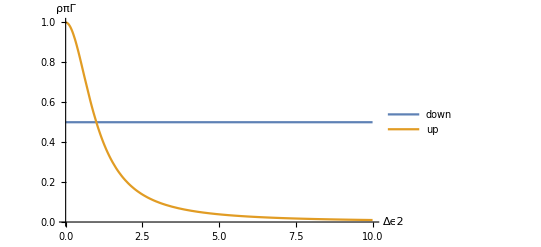

```mathematica
Plot[{-Im[DOS1[w+s,em,e2*G,e1, tdots,gamma2,gamma1,t2,t1]],-Im[DQD[w+s,e2,e1, tdots,gamma2,gamma1]] },{e2,0,10},PlotRange->{0,1}, AxesLabel->{Δϵ2 , ρπΓ}, PlotLegends->{"down","up"}]
```

```mathematica
G = 1
```

1

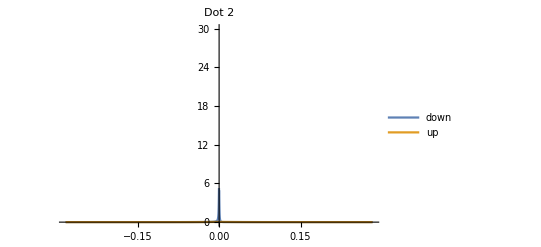

```mathematica
Plot[{-Im[DOS1[omega+s,em,e2,e1, tdots,gamma2,gamma1,t2,t1]/Pi] ,-Im[DQD[omega+s,e2,e1, tdots,gamma2,gamma1]/Pi]  },{omega,-10*G,10*G},PlotRange->{0,30},PlotLabel->"Dot 2",PlotLegends->{"down","up"}]
```

```mathematica
RealDigits[1.]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},1}

```mathematica
FullSimplify[DOS1[w,0,0,0, 0,γ,γ,2γ,2γ]/Pi, Assumptions->{γ>0}]
```

(w^3+3 ⅈ w^2 γ-14 w γ^2-16 ⅈ γ^3)/(π w (w+2 ⅈ γ) (w^2+2 ⅈ w γ-16 γ^2))

```mathematica
DOS1[w,0,0,0, 0,γ,γ,2γ,2γ]/Pi
```

1/(π (w+ⅈ γ+(γ Conjugate[γ])/(w+ⅈ γ)-((2 γ-(2 ⅈ γ √(γ^2))/(w+ⅈ γ)) (2 Conjugate[γ]-(2 ⅈ Conjugate[γ] √(Conjugate[γ]^2))/(w+ⅈ Conjugate[γ])))/(w-(8 γ Conjugate[γ])/(w+ⅈ γ)-((-2 γ+(2 ⅈ γ √(γ^2))/(w+ⅈ γ)) (-2 Conjugate[γ]+(2 ⅈ Conjugate[γ] √(Conjugate[γ]^2))/(w+ⅈ Conjugate[γ])))/(w+ⅈ γ+(γ Conjugate[γ])/(w+ⅈ γ)))))

```mathematica
Rationalize[G]
```

1

1

1.

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},1}

```mathematica
ToString[StringForm["/home/cifucito/nrgcode/TwoChNRG/Data/Gamma1=`1`,Gamma2=`2`,tdots=`3`,t1=`4`,t2=`5`",g1,g2,tt,m1,m2]]
```

```mathematica
ListPlot[Table[f,{f,{Sin[x],Cos[x]}},{x,0,2 π,0.1}],PlotLegends->{"sin(x)","cos(x)"}]
```

```mathematica
FullSimplify[DOS1[w,0,0,0, 0,Γ,Γ,0,0],Assumptions->{Γ>0,λ>0,ep1>0,ep2>0}]
```

(w+ⅈ Γ)/(w^2+2 ⅈ w Γ)

```mathematica
FullSimplify[Chop[DOS1[0.00001,0,ep1,ep2, 0,Γ,Γ,t1,t1],10^(-6)],Assumptions->{Γ>0,t1>0,ep1>0,ep2>0}]
```

$Aborted

```mathematica
+
```

```mathematica
DOS1[w,em,e1,e2, tdots,gamma1,gamma2,t1,t2]
```

1/(-e1+ⅈ gamma1+w-((tdots-ⅈ √(gamma1 Conjugate[gamma2])) (-ⅈ √(gamma2 Conjugate[gamma1])+Conjugate[tdots]))/(-e2+ⅈ gamma2+w)-(w (t1+(t2 (-ⅈ √(gamma1 gamma2)+tdots))/(-e2+ⅈ gamma2+w)) (Conjugate[t1]+(Conjugate[t2] (-ⅈ √(Conjugate[gamma1] Conjugate[gamma2])+Conjugate[tdots]))/(-e2+w+ⅈ Conjugate[gamma2])))/((em+w) (-em+w-1/(em+w)w ((t2 Conjugate[t2])/(-e2+ⅈ gamma2+w)+(t2 Conjugate[t2])/(e2+ⅈ gamma2+w)+((-t1-(t2 (-ⅈ √(gamma1 gamma2)-tdots))/(e2+ⅈ gamma2+w)) (-Conjugate[t1]-(Conjugate[t2] (-ⅈ √(Conjugate[gamma1] Conjugate[gamma2])-Conjugate[tdots]))/(e2+w+ⅈ Conjugate[gamma2])))/(e1+ⅈ gamma1+w-((-tdots-ⅈ √(gamma1 Conjugate[gamma2])) (-ⅈ √(gamma2 Conjugate[gamma1])-Conjugate[tdots]))/(e2+ⅈ gamma2+w))))))

```mathematica
FullSimplify[DOS1[w,0,e1,e2, tdots,Γ,0,0,t2]/Pi, Assumptions->{Γ>0,t2>0,tdots>0,ep1>0,ep2>0}]
```

1/(π (-e1+w+(tdots^2 (e2-w-t2^2/(w+(t2^2 (-tdots^2+2 w (e1+w+ⅈ Γ)))/((e2-w) (-tdots^2+(e2+w) (e1+w+ⅈ Γ))))))/(e2-w)^2+ⅈ Γ))

```mathematica
*M[Conjugate[tdots],Conjugate[Gamma1],Gamma2]
```

```mathematica
Manipulate[Grid[{{Plot[{-Im[DOS1[w+s,em,e1,e2, tdots,gamma1,gamma2,t1,t2]] ,-Im[DQD[w+s,e1,e2, tdots,gamma1,gamma2]]},{w,-a,a},PlotRange->{0,y },PlotLabel->"Dot 1"],Plot[{-Im[DOS1[w+s,em,e2,e1, tdots,gamma2,gamma1,t2,t1]] ,-Im[DQD[w+s,e1,e2, tdots,gamma2,gamma1]]},{w,-a,a},PlotRange->{0,y},PlotLabel->"Dot 2",PlotLegends->{"down","up"}]}}],{a,0.00001,10},{y,0.25/G,10/G},{gamma1,0,1*G,1*G}, {gamma2,0,4*G,G},{tdots,0,4*G},{t1, 0,4*G},{t2,0,4*G},{em,0,4*G},{e1,-10*G,10*G,1*G},{e2, -10*G,10*G,1*G} ]
```

```mathematica
Manipulate[Grid[{{Plot[{-Im[DOS1[w+s,em,e1,e2, tdots,gamma1,gamma2,t1,t2]/Pi] ,-Im[DQD[w+s,e1,e2, tdots,gamma1,gamma2]/Pi]},{w,-a,a},PlotRange->{0,y },PlotLabel->"Dot 1"],Plot[{-Im[DOS1[w+s,em,e2,e1, tdots,gamma2,gamma1,t2,t1]/Pi] ,-Im[DQD[w+s,e1,e2, tdots,gamma2,gamma1]/Pi]},{w,-a,a},PlotRange->{0,y},PlotLabel->"Dot 2",PlotLegends->{"down","up"}],Export[ToString[StringForm["/home/cifucito/nrgcode/TwoChNRG/Data/Green/Gamma1=`1`,Gamma2=`2`,tdots=`3`,t1=`4`,t2=`5`,em=`6`,e1=`7`,e2=`8`.dat",2*gamma1/G,2*gamma2/G,2*tdots/G,2*t1/G,2*t2/G,2*em/G,2*e1/G,2*e2/G]],Table[Im[(-DOS1[o+s,em,e1,e2, tdots,gamma1,gamma2,t1,t2])/Pi]],"Table"]}}],{a,10*G,10*G},{y,1/(Pi*G),1/(Pi*G)},{gamma1,0,1*G,1*G}, {gamma2,0,4*G,G/2.0},{tdots,0,4*G,G/2.0},{t1, 0,4*G,G/2.0},{t2,0,4*G,G*0.5},{em,0,4*G,G/2.0},{e1,-10*G,10*G,1*G},{e2, -10*G,10*G,1*G} ]
```